# Package

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Needs["MethodSugiyama`"]
```

```mathematica
?"MethodSugiyama`*"
```

# Help

## 0. GetGraph

```mathematica
g=GetGraph[10];
```

## 1. GetDaG - удаление циклов

```mathematica
GetDAG[g,ApproachOption->"Unkwnon"]
```

GetDAG::option: Option Unkwnon is not in list of options. Choose another one from the list: 
Random Order
BFS Order
DFS Order
VertexOutDegree Order
Cycle Removal
IP SCF
IP TI

$Aborted

```mathematica
GetDAG[g,ApproachOption->"Random Order"]
```

<|acyclic graph→{1->2,1->4,1->9,2->4,2->8,2->9,3->1,3->6,3->7,3->9,5->4,10->2,10->3,10->8,10->9},feedback set→{1->5,2->10,4->8,6->1,6->3,6->9,6->10,8->1,8->7,8->9,9->10}|>

```mathematica
GetDAG[g,ApproachOption->"BFS Order"]
```

<|acyclic graph→{1->2,1->4,1->5,1->9,2->4,2->8,2->9,2->10,3->6,4->8,8->7,9->10,10->3},feedback set→{3->1,3->7,3->9,5->4,6->1,6->3,6->9,6->10,8->1,8->9,10->2,10->8,10->9}|>

```mathematica
GetDAG[g,ApproachOption->"DFS Order"]
```

<|acyclic graph→{1->2,1->4,1->5,1->9,2->4,2->8,3->7,3->9,4->8,6->1,6->3,6->9,6->10,8->7,9->10,10->2,10->8},feedback set→{2->9,2->10,3->1,3->6,5->4,8->1,8->9,10->3,10->9}|>

```mathematica
GetDAG[g,ApproachOption->"VertexOutDegree Order"]
```

<|acyclic graph→{1->4,1->5,1->9,2->4,2->8,2->9,3->1,3->7,3->9,5->4,6->1,6->3,6->9,6->10,8->7,8->9,10->2,10->8,10->9},feedback set→{1->2,2->10,3->6,4->8,8->1,9->10,10->3}|>

```mathematica
step1=GetDAG[g,ApproachOption->"Cycle Removal"]
```

<|acyclic graph→{1->2,1->4,1->5,1->9,2->4,2->8,2->9,2->10,3->7,3->9,4->8,5->4,6->1,6->3,6->9,6->10,8->7,8->9,10->3,10->8,10->9},feedback set→{3->1,3->6,8->1,9->10,10->2}|>

```mathematica
GetDAG[g,ApproachOption->"IP SCF"]
```

<|acyclic graph→{1->2,1->4,1->5,1->9,2->4,2->8,2->9,3->1,3->7,3->9,4->8,5->4,6->1,6->3,6->9,6->10,8->7,8->9,10->2,10->3,10->8,10->9},feedback set→{2->10,3->6,8->1,9->10}|>

```mathematica
GetDAG[g,ApproachOption->"IP TI"]
```

<|acyclic graph→{1->2,1->4,1->5,1->9,2->4,2->8,2->9,2->10,3->6,3->7,3->9,4->8,5->4,6->9,8->9,10->8,10->9},feedback set→{3->1,6->1,6->3,6->10,8->1,8->7,9->10,10->2,10->3}|>

## 2. GetLayering

```mathematica
GetLayering[step1,ApproachOption->"Unknown"]
```

GetLayering::option: Option Unknown is not in list of options. Choose another one from the list: 
Longest Path
Exact
Min Width

$Aborted

```mathematica
step2=GetLayering[step1,ApproachOption->"Longest Path"]
```

<|acyclic graph→{1->2,1->4,1->5,1->9,2->4,2->8,2->9,2->10,3->7,3->9,4->8,5->4,6->1,6->3,6->9,6->10,8->7,8->9,10->3,10->8,10->9},feedback set→{3->1,3->6,8->1,9->10,10->2},layers→{{6},{1},{2,5},{4,10},{3,8},{7,9}}|>

```mathematica
GetLayering[step1,ApproachOption->"Exact"]
```

<|acyclic graph→{1->2,1->4,1->5,1->9,2->4,2->8,2->9,2->10,3->7,3->9,4->8,5->4,6->1,6->3,6->9,6->10,8->7,8->9,10->3,10->8,10->9},feedback set→{3->1,3->6,8->1,9->10,10->2},layers→{{6},{1},{2,5},{4,10},{3,8},{7,9}}|>

```mathematica
GetLayering[step1,ApproachOption->"Min Width"]
```

<|acyclic graph→{1->2,1->4,1->5,1->9,2->4,2->8,2->9,2->10,3->7,3->9,4->8,5->4,6->1,6->3,6->9,6->10,8->7,8->9,10->3,10->8,10->9},feedback set→{3->1,3->6,8->1,9->10,10->2},layers→{{6},{1},{2,5},{10,4},{3,8},{7,9}}|>

```mathematica
GetLayering[step1,ApproachOption->{"Min Width",20,10}]
```

<|acyclic graph→{1->2,1->4,1->5,1->9,2->4,2->8,2->9,2->10,3->7,3->9,4->8,5->4,6->1,6->3,6->9,6->10,8->7,8->9,10->3,10->8,10->9},feedback set→{3->1,3->6,8->1,9->10,10->2},layers→{{6},{1},{2,5},{10,4},{3,8},{7,9}}|>

```mathematica
GetLayering[step1,ApproachOption->{"Min Width",20,10},ImprovmentOption->"Unk"]
```

GetLayering::option: Option Unk is not in list of options. Choose another one from the list: 
True
False

$Aborted

```mathematica
GetLayering[step1,ApproachOption->{"Min Width",20,10},ImprovmentOption->True]
```

<|acyclic graph→{1->2,1->4,1->5,1->9,2->4,2->8,2->9,2->10,3->7,3->9,4->8,5->4,6->1,6->3,6->9,6->10,8->7,8->9,10->3,10->8,10->9},feedback set→{3->1,3->6,8->1,9->10,10->2},layers→{{6},{1},{2,5,4},{10,3,8},{7,9}}|>

```mathematica
GetLayering[step1,ApproachOption->{"Min Width",20,10},ImprovmentOption->False]
```

<|acyclic graph→{1->2,1->4,1->5,1->9,2->4,2->8,2->9,2->10,3->7,3->9,4->8,5->4,6->1,6->3,6->9,6->10,8->7,8->9,10->3,10->8,10->9},feedback set→{3->1,3->6,8->1,9->10,10->2},layers→{{6},{1},{2,5},{10,4},{3,8},{7,9}}|>

## 3. AddDummyVertices

```mathematica
AddDummyVertices[step2,ApproachOption->"Unk"]
```

AddDummyVertices::option: Option Unk is not in list of options. Choose another one from the list: 
Base
Cut

$Aborted

```mathematica
AddDummyVertices[step2,ApproachOption->"Base"]
```

<|acyclic graph→{1->2,1->4,1->5,1->9,2->4,2->8,2->9,2->10,3->7,3->9,4->8,5->4,6->1,6->3,6->9,6->10,8->7,8->9,10->3,10->8,10->9},feedback set→{3->1,3->6,8->1,9->10,10->2},graph with dummies→{1->2,1->5,2->4,2->10,3->7,3->9,4->8,5->4,6->1,8->7,8->9,10->3,10->8,1->11,11->4,1->12,12->13,13->14,14->9,2->15,15->8,2->16,16->17,17->9,6->18,18->19,19->20,20->3,6->21,21->22,22->23,23->24,24->9,6->25,25->26,26->10,10->27,27->9,1->28,28->29,29->3,1->30,30->31,31->8},layers with dummies→{{6},{1,18,21,25},{2,5,11,12,19,22,26,28,30},{4,10,13,15,16,20,23,29,31},{3,8,14,17,24,27},{7,9}},first dummy→11|>

```mathematica
step3=AddDummyVertices[step2,ApproachOption->"Cut"]
```

<|acyclic graph→{1->2,1->4,1->5,1->9,2->4,2->8,2->9,2->10,3->7,3->9,4->8,5->4,6->1,6->3,6->9,6->10,8->7,8->9,10->3,10->8,10->9},feedback set→{3->1,3->6,8->1,9->10,10->2},layers→{{6},{1},{2,5},{4,10},{3,8},{7,9}},first dummy→11,layers with dummies→{{6},{1,12,18,21},{2,5,11,13,16,19,22},{4,10,14,17,20},{3,8,15},{7,9}},graph with dummies→{1->2,1->5,2->4,2->10,3->7,3->9,4->8,5->4,6->1,8->7,8->9,10->3,10->8,1->11,11->4,1->13,2->14,6->12,10->15,12->13,13->14,14->15,15->9,2->17,1->16,16->17,17->8,6->18,1->19,18->19,19->20,20->3,6->21,21->22,22->10}|>

## 4. GetVertexOrder

```mathematica
GetVertexOrder[step3,ApproachOption->"Unk"]
```

GetVertexOrder::option: Option Unk is not in list of options. Choose another one from the list: 
Barycenter
Matheuristic
{Barycenter,maxNumberOfIterations_Integer?Positive}

$Aborted

```mathematica
GetVertexOrder[step3,ApproachOption->"Barycenter"]
```

<|acyclic graph→{1->2,1->4,1->5,1->9,2->4,2->8,2->9,2->10,3->7,3->9,4->8,5->4,6->1,6->3,6->9,6->10,8->7,8->9,10->3,10->8,10->9},feedback set→{3->1,3->6,8->1,9->10,10->2},graph with dummies→{1->2,1->5,2->4,2->10,3->7,3->9,4->8,5->4,6->1,8->7,8->9,10->3,10->8,1->11,11->4,1->13,2->14,6->12,10->15,12->13,13->14,14->15,15->9,2->17,1->16,16->17,17->8,6->18,1->19,18->19,19->20,20->3,6->21,21->22,22->10},layers with dummies→{{6},{1,21,18,12},{5,11,16,2,22,19,13},{4,17,10,20,14},{8,3,15},{7,9}},first dummy→11|>

```mathematica
GetVertexOrder[step3,ApproachOption->"Matheuristic"]
```

<|acyclic graph→{1->2,1->4,1->5,1->9,2->4,2->8,2->9,2->10,3->7,3->9,4->8,5->4,6->1,6->3,6->9,6->10,8->7,8->9,10->3,10->8,10->9},feedback set→{3->1,3->6,8->1,9->10,10->2},graph with dummies→{1->2,1->5,2->4,2->10,3->7,3->9,4->8,5->4,6->1,8->7,8->9,10->3,10->8,1->11,11->4,1->13,2->14,6->12,10->15,12->13,13->14,14->15,15->9,2->17,1->16,16->17,17->8,6->18,1->19,18->19,19->20,20->3,6->21,21->22,22->10},layers with dummies→{{6},{1,12,18,21},{16,11,5,2,13,19,22},{17,4,14,20,10},{8,15,3},{7,9}},first dummy→11|>

```mathematica
step4=GetVertexOrder[step3,ApproachOption->{"Barycenter",10}]
```

<|acyclic graph→{1->2,1->4,1->5,1->9,2->4,2->8,2->9,2->10,3->7,3->9,4->8,5->4,6->1,6->3,6->9,6->10,8->7,8->9,10->3,10->8,10->9},feedback set→{3->1,3->6,8->1,9->10,10->2},graph with dummies→{1->2,1->5,2->4,2->10,3->7,3->9,4->8,5->4,6->1,8->7,8->9,10->3,10->8,1->11,11->4,1->13,2->14,6->12,10->15,12->13,13->14,14->15,15->9,2->17,1->16,16->17,17->8,6->18,1->19,18->19,19->20,20->3,6->21,21->22,22->10},layers with dummies→{{6},{1,21,18,12},{5,11,16,2,22,19,13},{4,17,10,20,14},{8,3,15},{7,9}},first dummy→11|>

## 5. GetCoordinates

```mathematica
GetCoordinates[step4,YDistanceOption->1,XDistanceOption->-1.3,WeightsOption->{1,1,1}]
```

GetCoordinates::option: 
Value -1.3 is not positive real.

$Aborted

```mathematica
GetCoordinates[step4,YDistanceOption->-1.4,XDistanceOption->-1.3,WeightsOption->{1,1,1}]
```

GetCoordinates::option: 
Value -1.4 is not positive real.

$Aborted

```mathematica
GetCoordinates[step4,YDistanceOption->1.3,XDistanceOption->1.8,WeightsOption->{1.3,1,1}]
```

GetCoordinates::option2: 
 {1.3,1,1} is not valid input weights. Please write in this form: {w1, w2, w3}

$Aborted

```mathematica
step5=GetCoordinates[step4,YDistanceOption->1,XDistanceOption->1,WeightsOption->{1,1,1}]
```

<|acyclic graph→{1->2,1->4,1->5,1->9,2->4,2->8,2->9,2->10,3->7,3->9,4->8,5->4,6->1,6->3,6->9,6->10,8->7,8->9,10->3,10->8,10->9},feedback set→{3->1,3->6,8->1,9->10,10->2},graph with dummies→{1->2,1->5,2->4,2->10,3->7,3->9,4->8,5->4,6->1,8->7,8->9,10->3,10->8,1->11,11->4,1->13,2->14,6->12,10->15,12->13,13->14,14->15,15->9,2->17,1->16,16->17,17->8,6->18,1->19,18->19,19->20,20->3,6->21,21->22,22->10},layers with dummies→{{6},{1,21,18,12},{5,11,16,2,22,19,13},{4,17,10,20,14},{8,3,15},{7,9}},coords→{6→{-4,-1},1→{-3,-2},21→{-4,-2},18→{-5,-2},12→{-6,-2},5→{0,-3},11→{-1,-3},16→{-2,-3},2→{-3,-3},22→{-4,-3},19→{-5,-3},13→{-6,-3},4→{-2,-4},17→{-3,-4},10→{-4,-4},20→{-5,-4},14→{-6,-4},8→{-3,-5},3→{-4,-5},15→{-5,-5},7→{-3,-6},9→{-4,-6}}|>

## 6. Итоговая функция

Done GetDag

Done GetLayering

Done GetAddDummyVertics

Done GetVertexOrder

Done GetCoords

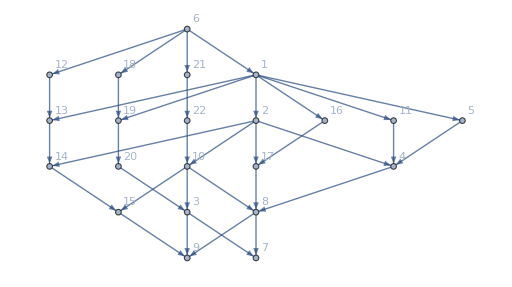

```mathematica
input=<|
"GetDag"-><|"ApproachOption"->"Cycle Removal"|>, 
"GetLayering"-> <|"ApproachOption"->"Longest Path",
                                    "ImprovmentOption"->False|>,
"AddDummyVertices"-><|"ApproachOption"->"Cut"|>,
"GetVertexOrder"-><|"ApproachOption"->{"Barycenter",5}|>,
"GetCoordinates"-> <|"YDistanceOption"->1,
                                           "XDistanceOption"->1.5,
                                            "WeightsOption"->{1,1,1}|>
|>;
res=MyLayeredGraphPlot[g,input,ApproachOption->"WM"]
```

```mathematica
Graph
```